# Option Pricing Notes

Stocks:
* Issued by firms to finance operations.
* Represent ownership of the firm.
* Price known today, but not in the future.
* May or may not pay dividends.

Bond:
*Price known today.
*Future pay offs known at fixed dates.
*Otherwise, the price movement is random.
*Final payoff at maturity: face vale/nominal value/principal.
*Intermediate payoffs: coupons.
*Exposed to default/credit risk.

Derivatives (Basic Securities):
*Sell for a price/value/premium today.
*Future value derived from the value of underlying securities.
*Tared at exchanges - standardized contract, no credit risk.
*or, over-the-counter(OTC)- a network of dealers and institutions, can be non-standard, some credit risk.

Forward Contract:
*An agreement to buy (long) or sell (short) a given underlying asset S: 
-At predetermined future date T  (maturity).
-At a predetermined price F (forward price).
*F is chosen so that the contract has zero value today.

## Call and Put options

Vanilla options:
*Call option: a right to buy the underlying.
*Put option: a right to sell the underlying.
*European option: the right can be exercised only at maturity.
*American option: can be exercised at any time before maturity.

Exotic options: 
*Asian options: the payoff depends of the average underlying asset price.
*Lookback options: the payoff depends on the maximum r minimum of the underlying asset price.
*Barrier option: the payoff depends on whether the underlying crossed a barrier or not
*Basket options: the payoff depends on the value of several underlying assets.

## Brownian motion process

History
*Brown, 1800’s.
*Bachelier, 1900.
*Einstein, 1905, 1906.
*Wiener, Levy 1920.b4s, 30.b4s.
*Ito, 1940.b4s.
*Samuelson, 1960.b4s.
*Merton, Black, Scholes, 1970.b4s.

#### Short introduction to the Merton-Black-Scholes model

Risk-free asset : B (t) = e^(r t)

Stock has a log normal distribution:   log S(t)=log S(0)+ (μ-1/2 σ^2) t+σ √t z(t)

where z (t) is a standard normal random variable. Thus,                           S(t) = S(0)  e^((μ-1/2 σ^2) t+σ √t z(t))

and it can be shown that: ES(t)=S(0)e^(μ t), 1/2 Var [log (S(t))/(S(0))]=σ^2

#### Discretized Brownian motion

W(0) =0

W(t_(k+1) ) = W(t_k) + √Δt z(t_k) , where z(t_k) are independent standard normal random variables (with μ = 0 and σ^2 = 1) .

W(t_l)-W(t_k) =√Δt∑_(i=k)^(l-1) z(t_i)  , is normally distribute, with zero mean and variance (l-k)Δt=t_l-t_k

The process W is called a Random walk process.

In the limit when Δt goes to zero, it can be shown that the random walk converges to a Brownian motion, denoted by W.

#### Brownian motion definition

W(t)-W(s) is normally distribute, with zero mean and variance t-s, for s<t.

The process W has independent increments: for any set of times 0 ≤ t_1 < t_2 ···< t_n, the random variables: W(t_2)-W(t_1),W(t_3)-W(t_2),... ,W(t_n)-W(t_(n-1))  are independent.

Normalization W(0) =0

The sample paths {W(t); t≥ 0 } are continuous functions of t.

So there is no jumps on Brownian motion models, the prices are continuous.

Example Code

```mathematica
Data=RandomFunction[RandomWalkProcess[1/2],{0,100}];
```

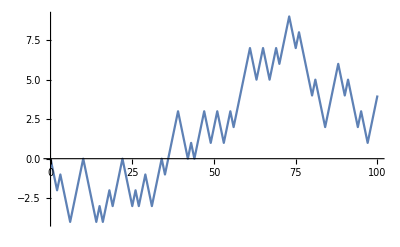

```mathematica
ListLinePlot[Data]
```

Not differentiable E [W(t) - W(s)]^2/(t-s)^2=1/(t-s)→∞ as (t-s) →0.

A Markovian process: the distribution of the future value W(t) given information up to time  s<t depends only on W(s) and not on the past values.

Martingale property:  E_s W(t) = W(s) , t >s because E_s W(t)  =E [ W(t)- W(s)|W(s) ] →0+  E [W(s)|W(s) ] = E [ W(t)- W(s) ] + W(s)  = W(s)

## Stochastic Differential Equations

Modeling a process in time with an ODE:

(d X(t))/dt= μ(t, X(t))

informally written as: 
d X(t)= μ(t, X(t)) dt

We add a random component to the Stochastic differential equation (SDE):

d X(t)= μ(t, X(t)) dt + σ (t, X(t)) dW(t)

In the integral form:

∫_0^t X(s)ⅆs=  ∫_0^t μ(s, X(s))  ⅆs+ ∫_0^t σ (s, X(s))ⅆs dW(s)

X(t)= X(0)+ ∫_0^t μ(s, X(s))  ⅆs+ ∫_0^t σ (s, X(s))ⅆs dW(s)

#### Itô Integral

Fix a process Y adapted to the information given by W, such that:

E[ ∫_0^t Y^2(U)  ⅆu]<∞

Construction: Split interval [0, t] into n subintervals [t_i, t_(i+1)] and consider

I_n(t) := Σ_iY(t_i) [W(t_(i+1)) - W(t_i)]

Ito showed that there is a limit I(t),

E[(I_n(t) - I_n(t))^2 ] →0

And called the limit the stochastic integral:

I(t)= ∫_0^t Y(s)ⅆ W(s)
Example: 
Y(s) → number of shares that change in time.
ⅆ W(s) → change of the stock price.
Gain process keeping Y(s) as the money is Y of s the times W(s) changes.

#### Stochastic Integral properties

Process I(t)= ∫_0^t Y(u)ⅆ W(u) is a martingale with mean zero, or

E[∫_0^t Y(u)ⅆ W(u)] = 0
E_s[∫_0^t Y(u)ⅆ W(u)] = ∫_0^s Y(u)ⅆ W(u)

And the variance is:

E[(∫_0^t Y(u)ⅆ W(u))^2] = E[∫_0^s Y^2(u)ⅆu]

If your stock prices is a martingale , your gains and losses from that stock should be also a martingale.

#### Ito’s Rule

Standard calculus:

d/dt f(t,x(t)) =∂/(∂t)f(t,x(t))  +∂/(∂x)f(t,x(t)) ⅆ/ⅆt x(t)

or, denoting partial derivatives with subscripts,

df(t,x(t)) =f_t(t,x(t)) dt +f_x(t,x(t)) dx(t)

In stochastic calculus, for

d X (t) =μ (t) dt + σ(t)dW(t)
df (t,X (t)) =f_t(t,X(t)) dt +f_x(t,X(t)) dX(t)+ 1/2 σ^2 f_xx(t,X(t)) dt

or

df =[f_t+μ f_x dx(t) +1/2 σ^2 f_xx] dt +σ f_x dW

Ito’s rule.- how the option price behaves as a function of the stock price.